# VQE run of H_2 on Superconducting Qubits

## VQD setup

Set the main directory as the current directory, env variable

```mathematica
SetDirectory[NotebookDirectory[]];
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Quiet[Import["https://qtechtheory.org/questlink.m"]]
```

This will download a binary file  quest_link from the repo

```mathematica
CreateDownloadedQuESTEnv[];
```

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
Get["../../vqd.wl"]
```

Evaluate source_vqd.nb !

## Architecture of the virtual superconducting qubits

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
QubitNum->4,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
(*Standard T1, T2 passive noise *)
StdPassiveNoise->True,
(* Residual capacitive coupling *)
ZZPassiveNoise->True
};
```

## Modify the device

```mathematica
dev=SuperconductingHub[ExchangeCoupling-><|1<->2->1.5,0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4|>];
```

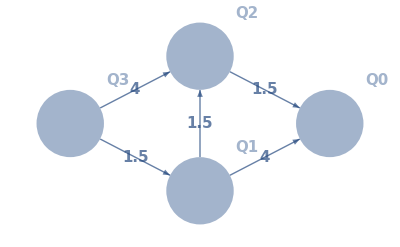

```mathematica
dev[Connectivity]
```

## The exact solution

```mathematica
{hamiltonian, nterms, nq} = FormatHamiltonian["H2.txt"]
```

{-0.109731 Id_3-0.0454429 X_2 X_3 Y_0 Y_1+0.0454429 X_0 X_3 Y_1 Y_2+0.0454429 X_1 X_2 Y_0 Y_3-0.0454429 X_0 X_1 Y_2 Y_3+0.169885 Z_0+0.169885 Z_1+0.168212 Z_0 Z_1-0.218863 Z_2+0.120051 Z_0 Z_2+0.165494 Z_1 Z_2-0.218863 Z_3+0.165494 Z_0 Z_3+0.120051 Z_1 Z_3+0.173954 Z_2 Z_3,15,4}

```mathematica
groundstate=Min@Eigenvalues@CalcPauliStringMatrix@hamiltonian
```

-1.13712

## VQE: H_2 -Graphics-

Set the device and VQE config

Create VQE function with args: hamiltonian, device, ansatz, energy
Nice monitor plot

```mathematica
vqeconf=DefaultConfig[dev,hamiltonian];
```

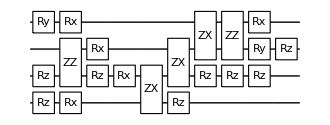

```mathematica
ansatz=RandomAnsatz[vqeconf,20];
DrawCircuit[%,4]
```

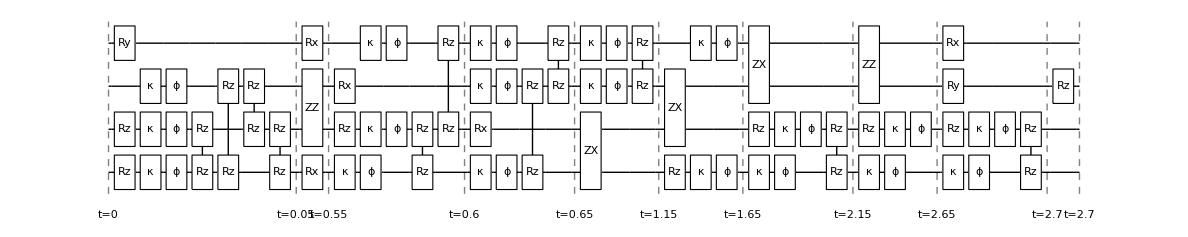

```mathematica
DrawCircuit[InsertCircuitNoise[ansatz,dev]]
```

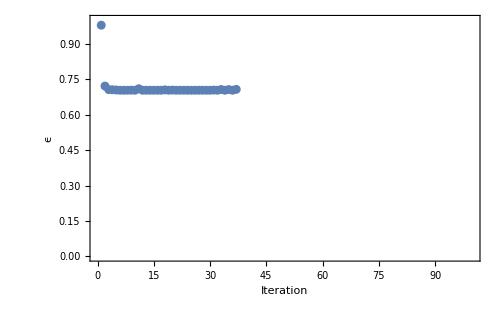

ϵ_final=0.70714

{Ry_3[0.210279],Rz_1[-0.183433],ZZ_(1,2),Rz_0[0.685482],Rz_1[0.755081],Rx_2[-0.750278],Rx_0[1.58758],Rx_1[0.257167],Rx_3[0.0510689],ZX_(1,0),ZX_(1,2),ZX_(3,2),ZZ_(2,3),Rz_1[0.639333],Rx_3[-0.0154007],Rz_0[-0.287802],Rz_1[-0.282206],Ry_2[-0.637263],Rz_2[-0.490948],Rz_1[-0.943176]}

```mathematica
VQE[hamiltonian,dev, ansatz]
```

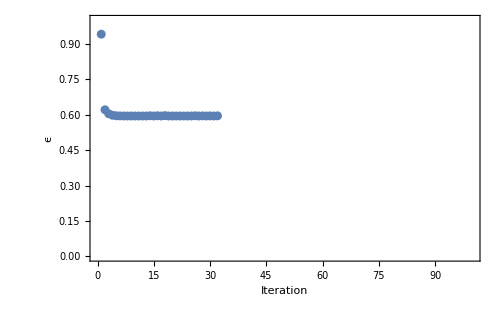

ϵ_final=0.595074

{Ry_3[-0.0122205],Rz_1[-0.727316],ZZ_(1,2),Rz_0[0.244034],Rz_1[-0.564099],Rx_2[0.286291],Rx_0[1.59025],Rx_1[0.226938],Rx_3[0.0961114],ZX_(1,0),ZX_(1,2),ZX_(3,2),ZZ_(2,3),Rz_1[0.214514],Rx_3[0.0321759],Rz_0[-0.469019],Rz_1[0.0727748],Ry_2[0.0907602],Rz_2[-0.117051],Rz_1[0.533032]}

```mathematica
VQE[hamiltonian,dev, ansatz,Noisy->False]
```